```mathematica
{-e-2*d1/a^3==v/v0*a1,e+d1/a^2==a1*a}
```

{(2 d1)/a^3-e==(a1 v)/v0,d1/a^2+e==a a1}

```mathematica
Solve[{-e-2*d1/a^3==v/v0*a1,-e+d1/a^3==a1},{a1,d1},Reals]//Simplify
```

{{a1→-(3 e v0)/(v+2 v0),d1→(a^3 e (v-v0))/(v+2 v0)}}

```mathematica
f1[r_,θ_]:=-3*1/(8+2)*10*r*Cos[θ]
f2[r_,θ_]:=-10*r*Cos[θ]+(1^3*10(8-1))/(8+2)*Cos[θ]
```

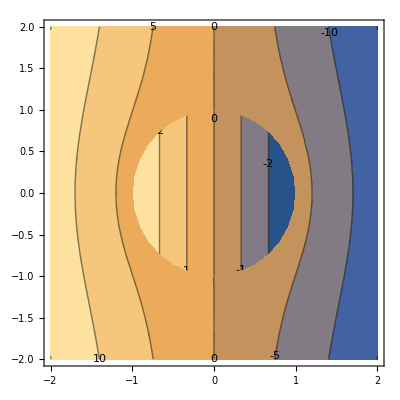

```mathematica
Show[{ContourPlot[f1[√(x^2+y^2),ArcTan[x,y]],
{x,y}∈Disk[{0,0},1],ContourLabels->True],
ContourPlot[f2[√(x^2+y^2),ArcTan[x,y]],
{x,y}∈RegionDifference[Polygon[{{-2,2},{2,2},{2,-2},{-2,-2}}],Disk[{0,0},1]],
ContourLabels->True
]
},PlotRange-> All]
```

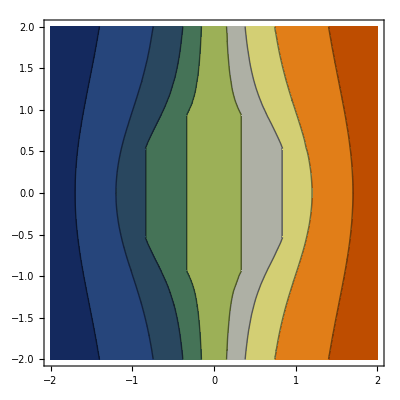

```mathematica
c=ColorData[40,"ColorList"];
Show[{ContourPlot[f1[√(x^2+y^2),ArcTan[x,y]],
{x,y}∈Disk[{0,0},1],Contours -> {-1,-2.5,-5,-10,1,2.5,5,10},
ContourShading->c],
ContourPlot[f2[√(x^2+y^2),ArcTan[x,y]],
{x,y}∈RegionDifference[Polygon[{{-2,2},{2,2},{2,-2},{-2,-2}}],Disk[{0,0},1]],
Contours -> {-1,-2.5,-5,-10,1,2.5,5,10},
ContourShading->c
]
},PlotRange-> All]
```

```mathematica
Plot3D[f1[x,y]]
```

```mathematica
FromPolarCoordinates[{r,θ}]
```

{r Cos[θ],r Sin[θ]}

```mathematica
Solve[{-e-2*d1/a^3==a1,-e+d1/a^3==a1},{a1,d1},Reals]//Simplify
```

{{a1→-e,d1→0}}

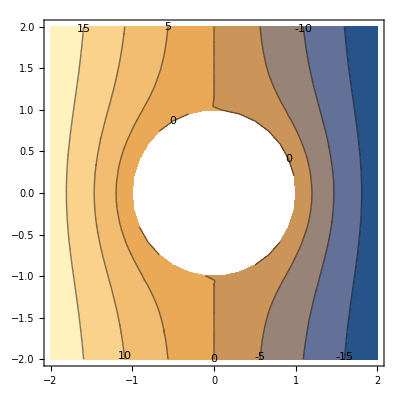

```mathematica
f3[r_,θ_]:=-10*r*Cos[θ]+(10*1^3)/r^2*Cos[θ];
ContourPlot[f3[√(x^2+y^2),ArcTan[x,y]],
{x,y}∈RegionDifference[Polygon[{{-2,2},{2,2},{2,-2},{-2,-2}}],Disk[{0,0},1]],ContourLabels->True]
```